```mathematica
CruchenieRyad[x_, y_, a_, b_, N_]:=
Module[{res, i, j},
res = 0;
For[i:=1, i<=N, i+=2,
For[j:= 1, j <=N, j+=2,
res+=(Sin[(i*Pi*x)/a]*Sin[(j*Pi*y)/b])/(i j (b^2 i^2+a^2 j^2));
];
];
Return[res];
 ];
```

-Graphics3D-

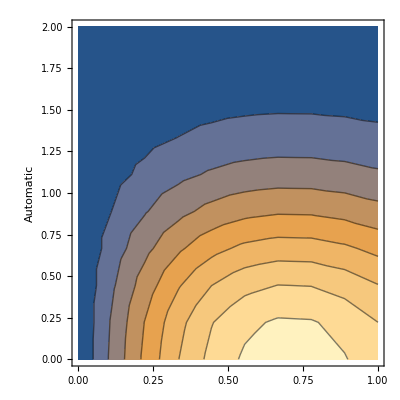

```mathematica
Module[{a, b, G, thetha, n, vectX, vectY, coordZ, X, Y},
a=1;b=2;G=0.1;thetha = 0.5;n=10;
vectX = Array[#&,n,{0,a}];
vectY = Array[#&,n,{0,b}];
coordZ= ConstantArray[0,{n, n}];
For[i:=1, i <=n, ++i,
For[j :=1, j <=n, ++j,
coordZ[[i]][[j]]=CruchenieRyad[vectX[[i]], vectY[[j]], a, b, n];
]
];
coordZ*=(32*G*thetha*a^2*b^2)/Pi^4;
{X, Y} = {ConstantArray[vectX,Length[vectX]],Transpose@ConstantArray[vectY,Length[vectY]]};
X*Exp[-X^2-Y^2];
Print[ListPlot3D[Flatten[{X,Y,X*Exp[-X^2-Y^2]},{2,3}], PlotRange -> All, AxesLabel -> Automatic, 
           ImagePadding -> 20, Mesh -> 35, InterpolationOrder -> 2, 
           ColorFunction -> "Rainbow", Boxed -> False]]
Print[ListContourPlot[Flatten[{X,Y,X*Exp[-X^2-Y^2]},{2,3}], PlotRange -> All, AxesLabel -> Automatic, 
           ImagePadding -> 20, Mesh -> 35, InterpolationOrder -> 2]];
];
```

```mathematica
Module[{a, b, G, thetha, n, a1, a2, a3, u, vectX, vectY, coordZ},
a=1;b=2;G=0.1;thetha = 0.5;n=10;

d = 16*(45 a^6+509 a^2 b^2(a^2+b^2)+45*b^6);
a1=35*(9 a^4+130 a^2 b^2+9 b^4)/d;
a2=105(9*a^2+b^2)/d;
a3=105(a^2+9 b^2)/d;

u[x_, y_]:=(x^2-a^2)*(y^2-b^2)*(a1+a2*x^2+a3*y^2);

vectX = Array[#&,n,{0,a}];
vectY = Array[#&,n,{0,b}];
coordZ= ConstantArray[0,{n, n}];

For[i:=1, i <=n, ++i,
For[j :=1, j <=n, ++j,
coordZ[[i]][[j]]=u[vectX[[i]], vectY[[j]]];
]
];

coordZ*=2G*thetha;

{X, Y} = {ConstantArray[vectX,Length[vectX]],Transpose@ConstantArray[vectY,Length[vectY]]};
X*Exp[-X^2-Y^2];
Print[ListPlot3D[Flatten[{X,Y,X*Exp[-X^2-Y^2]},{2,3}], PlotRange -> All, AxesLabel -> Automatic, 
           ImagePadding -> 20, Mesh -> 35, InterpolationOrder -> 2, 
           ColorFunction -> "Rainbow", Boxed -> False]]
Print[ListContourPlot[Flatten[{X,Y,X*Exp[-X^2-Y^2]},{2,3}], PlotRange -> All, AxesLabel -> Automatic, 
           ImagePadding -> 20, Mesh -> 35, InterpolationOrder -> 2]];
];
```

-Graphics3D-

-Graphics-